```mathematica
x=Cos[3π t]/5;
y=0.4Sin[3π t];
```

```mathematica
Vx=D[x,{t,1}];Print["Vx = " ,Vx];
Vy=D[y,{t,1}];Print["Vy = " ,Vy];
V=√(Vx^2+Vy^2)//Simplify;Print["V = ",V];
```

Vx = -3/5 π Sin[3 π t]

Vy = 3.76991 Cos[3 π t]

V = √(14.2122 Cos[3 π t]^2+3.55306 Sin[3 π t]^2)

```mathematica
Wx=FullSimplify[D[x,{t,2}]];Print["Wx = " ,Wx];
Wy=D[y,{t,2}];Print["Wy = " ,Wy];
W=√((Wx^2+Wy^2)//Expand//FullSimplify);Print["W = ",W];
```

Wx = -9/5 π^2 Cos[3 π t]

Wy = -35.5306 Sin[3 π t]

W = √(789.014-473.408 Cos[6 π t])

```mathematica
Wτ=((Vx+Wx+Vy+Wy)//FullSimplify)/(√(Vx^2+Vy^2))//FullSimplify;
Print["Wτ = ",Wτ];
Wn=√(W^2-Wτ^2)//FullSimplify;Print["Wn = ",Wn];
ρ=V^2/Wn//Simplify;Print["ρ = ",ρ];
```

Wτ = (-13.9954 Cos[3 π t]-37.4155 Sin[3 π t])/(√(8.88264+5.32959 Cos[6 π t]))

Wn = √((928.608+112.959 Cos[6 π t]-236.704 Cos[12 π t]-98.2524 Sin[6 π t])/(1.66667+1. Cos[6 π t]))

ρ = (14.2122 Cos[3 π t]^2+3.55306 Sin[3 π t]^2)/(√((928.608+112.959 Cos[6 π t]-236.704 Cos[12 π t]-98.2524 Sin[6 π t])/(1.66667+1. Cos[6 π t])))

```mathematica
Vxt=Vx/.t->1/6//N;Print["(при t =1/6): Vx = ",Vxt];
Vyt=Vy/.t->1/6//N;Print["(при t =1/6): Vy = ",Vxt];
Wxt=Wx/.t->1/6//N;Print["(при t =1/6): Wx = ",Wxt];
Wyt=Wy/.t->1/6//N;Print["(при t =1/6): Wy = ",Wyt];
Vt=V/.t->1/6//N;Print["(при t =1/6): V = ",Vt];
Wt=W/.t->1/6//N;Print["(при t =1/6): W = ",Wt];
Wnt=Wn/.t->1/6//N;Print["(при t =1/6): Wn = ",Wnt];
Wτt=Wτ/.t->1/6//N;Print["(при t =1/6): Wτ = ",Wτt];
ρt=ρ/.t->1/6//N;Print["(при t =1/6): ρ = ",ρt];
```

(при t =1/6): Vx = -1.88496

(при t =1/6): Vy = -1.88496

(при t =1/6): Wx = 0.

(при t =1/6): Wy = -35.5306

(при t =1/6): V = 1.88496

(при t =1/6): W = 35.5306

(при t =1/6): Wn = 29.4689

(при t =1/6): Wτ = -19.8496

(при t =1/6): ρ = 0.12057

```mathematica
points={};
xt=x/.t->0//N;yt=y/.t->0//N;
AppendTo[points,{xt,yt}];
Print["M_0: (t=0): x = ",xt,"; y = ",yt];
xt=x/.t->1/30//N;yt=y/.t->1/30//N;
AppendTo[points,{xt,yt}];
Print["M_1: (t=1/30): x = ",xt,"; y = ",yt];
xt=x/.t->1/24//N;yt=y/.t->1/24//N;
AppendTo[points,{xt,yt}];
Print["M_2: (t=1/24): x = ",xt,"; y = ",yt];
xt=x/.t->1/18//N;yt=y/.t->1/18//N;
AppendTo[points,{xt,yt}];
Print["M_3: (t=1/18): x = ",xt,"; y = ",yt];
xt=x/.t->1/12//N;yt=y/.t->1/12//N;
AppendTo[points,{xt,yt}];
Print["M_4: (t=1/12): x = ",xt,"; y = ",yt];
xt=x/.t->1/6//N;yt=y/.t->1/6//N;
AppendTo[points,{xt,yt}];
Print["M_5: (t=1/6): x = ",xt,"; y = ",yt];
```

M_0: (t=0): x = 0.2; y = 0.

M_1: (t=1/30): x = 0.190211; y = 0.123607

M_2: (t=1/24): x = 0.184776; y = 0.153073

M_3: (t=1/18): x = 0.173205; y = 0.2

M_4: (t=1/12): x = 0.141421; y = 0.282843

M_5: (t=1/6): x = 0.; y = 0.4

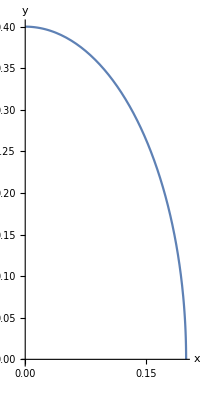

```mathematica
ParametricPlot[{Cos[3π t]/5,0.4Sin[3π t]},{t,0,1/6},AxesLabel->{"x","y"},PlotLegends->"Expressions"]
```